```mathematica
Select[d,#=={0,0}&]
```

{}

```mathematica
Position[d,{0.,0.}]
```

{}

```mathematica
ArcCos[1.-2*Sin[(-Pi/6+Pi/8)/2]^2]
```

0.1309

```mathematica
Pi/6.
```

0.523599

```mathematica
Pi/8.
```

0.392699

```mathematica
-Pi/4.
```

-0.785398

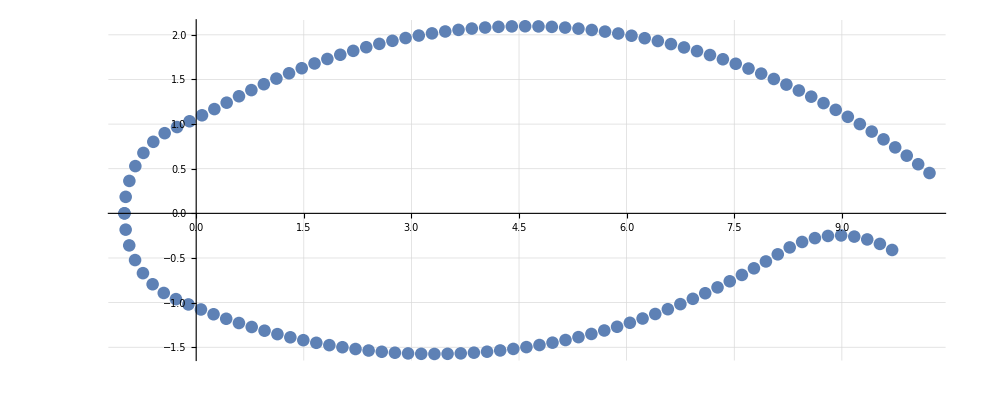

```mathematica
d = Import["out_data.txt","Table"];
l=ListPlot[d,AspectRatio->{1,1}, PlotRange->All, GridLines->Automatic]
```

```mathematica
par={Pi/6.,-Pi/8.,0.12,Pi/6.,-Pi/8.,0.12};
```

```mathematica
Write["in.txt",#]&/@par
```

{Null,Null,Null,Null,Null,Null}

```mathematica
FilePrint["in.txt"]
```

0.5235987755982988
-0.39269908169872414
0.12
0.5235987755982988
-0.39269908169872414
0.12

```mathematica
Close["in.txt"];
```

```mathematica
Run["./air_v2 < in.txt"]
```

0

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sur/Documents/TaskDash/Air

```mathematica
d = Import["out_data.txt","Table"];
```

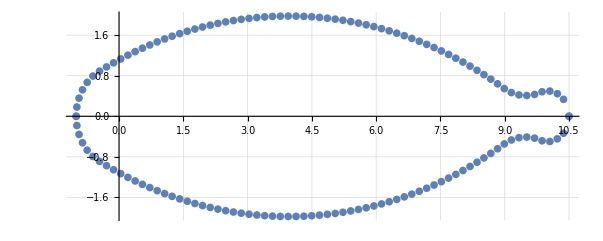

```mathematica
ListPlot[d,AspectRatio->{1,1}, GridLines->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[par_]:=Block[{},
Write["in.txt",#]&/@par;
Close["in.txt"];
Run["./air_v3 < in.txt"];
d = Import["out_data.txt","Table"];
l=ListPlot[d,AspectRatio->{1,1}, PlotRange->All, GridLines->Automatic];
l
]
```

```mathematica
gMax[alp_,bet_]:=ArcCos[1.-2*Sin[(alp+bet)/2]^2]
```

```mathematica
check[d_]:=Block[{},
eps=10^-4;
n =Length[d];
up=d[[;;n/2]];
down=d[[-1;;n/2+1;;-1]];
flag=0;
Do[
vec=up[[i]]-down[[i]];
If[vec[[2]]<-eps,flag=1;Break[]]
,{i,n/2}];
flag
]
```

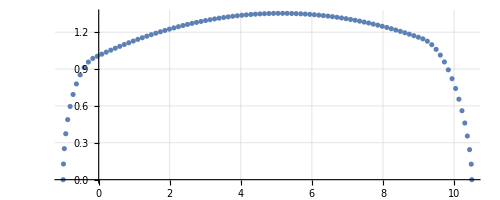
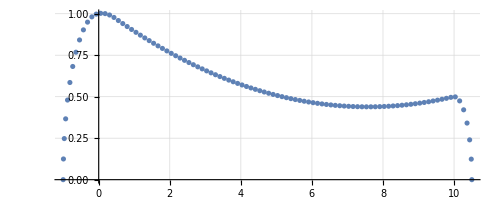
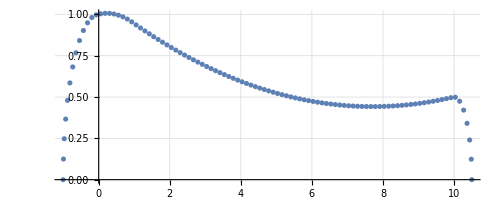
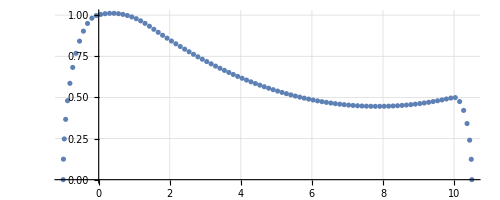
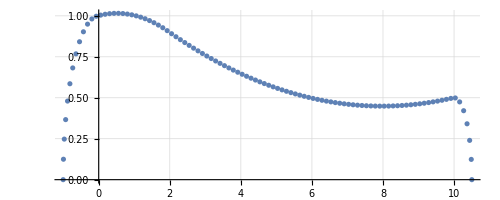
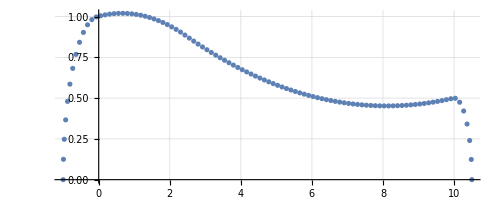
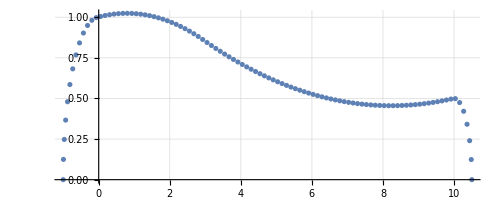
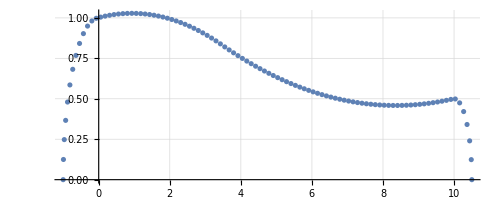

```mathematica
alp1 = .11;bet1=-0.1;
alp2 = -Pi/6.;bet2=-Pi/8.;
gam2 = 0.003;
Reap[Do[Sow[
f[{alp1,bet1,gam1,alp2,bet2,gam2}]],{gam1,0.000001,gMax[alp1,bet1],gMax[alp1,bet1]/20}]][[2,1]]
```

```mathematica
alp1 = -Pi/6.;bet1=Pi/3.;
alp2 = Pi/6.;bet2=-Pi/8.;
gam2 = 0.07;
mesh=Reap[Do[
Do[
f[{alp1,bet1,gam1,alp2,bet2,gam2}];Sow[{{gam1,alp1},check[d]}],{gam1,0.01,gMax[alp1,bet1],0.05}],{alp1,-Pi/3.,Pi/2.5,0.05 Pi}]][[2,1]];
```

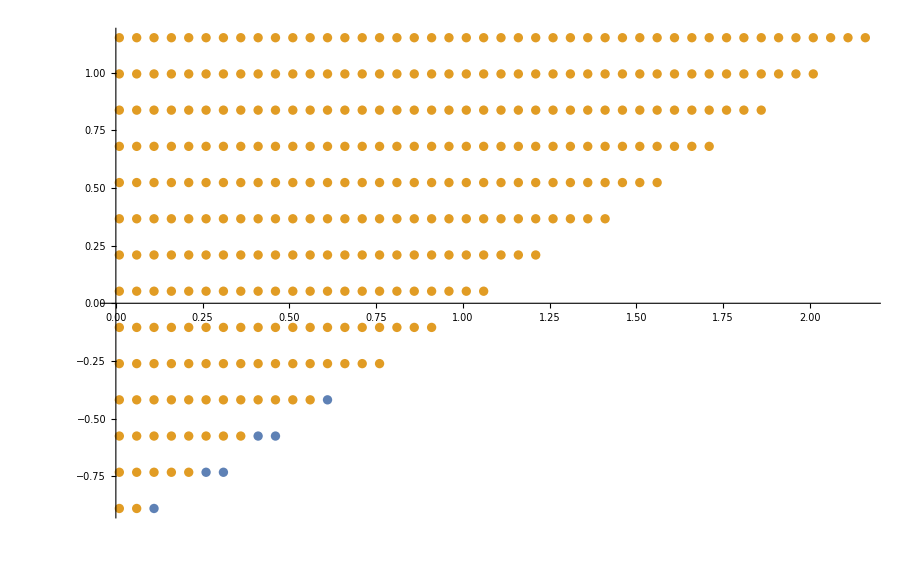

```mathematica
bad=Select[mesh,#[[2]]==1&][[;;,1]];good=Select[mesh,#[[2]]==0&][[;;,1]];
ListPlot[{bad,good}]
```

```mathematica
alp1 = -Pi/6.;bet1=Pi/3.;
alp2 = Pi/6.;bet2=-Pi/8.;
gam2 = 0.07;
mesh=Reap[
Do[
Do[
Do[
f[{alp1,bet1,gam1,alp2,bet2,gam2}];Sow[{{gam1,alp1, bet1},check[d]}],{gam1,0.01,gMax[alp1,bet1],0.05}],{alp1,-Pi/3.,Pi/2.5,0.05 Pi}],{bet1,-Pi/3.1,Pi/3.,0.05 Pi}]][[2,1]];
```

```mathematica
bad=Select[mesh,#[[2]]==1&][[;;,1]];good=Select[mesh,#[[2]]==0&][[;;,1]];
ListPointPlot3D[{bad,good},AxesLabel->{"gam","alp","bet"}]
```

-Graphics3D-

```mathematica
alp1 = -Pi/6.;bet1=Pi/3.;
alp2 = -Pi/6.;bet2=-Pi/8.;
gam2 = 0.003;
mesh=Reap[
Do[
Do[
Do[
f[{alp1,bet1,gam1,alp2,bet2,gam2}];Sow[{{gam1,alp1, bet1},check[d]}],{gam1,0.01,gMax[alp1,bet1],0.05}],{alp1,-Pi/3.,Pi/2.5,0.05 Pi}],{bet1,-Pi/3.1,Pi/3.,0.05 Pi}]][[2,1]];
```

```mathematica
bad=Select[mesh,#[[2]]==1&][[;;,1]];good=Select[mesh,#[[2]]==0&][[;;,1]];
ListPointPlot3D[{bad,good},AxesLabel->{"gam","alp","bet"}]
```

-Graphics3D-

```mathematica
checkCurve[d_]:=Block[{},
l=20/50.;
flag=0;
Do[
If[Norm[d[[i]]-d[[i+1]]]>l,flag=1;Break[]]
,{i,Length[d]-1}];
flag
]
```

```mathematica
checkCurve[d]
```

0

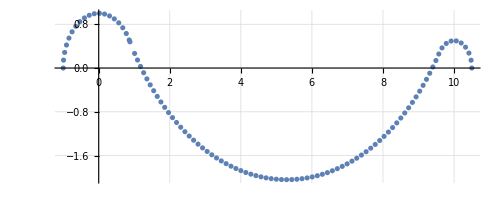
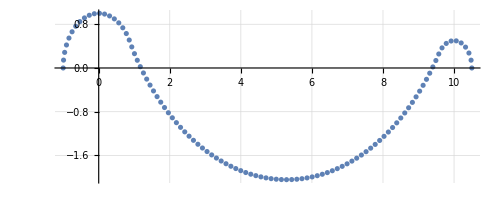
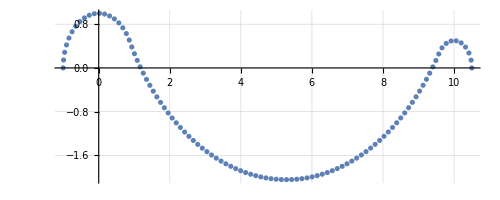
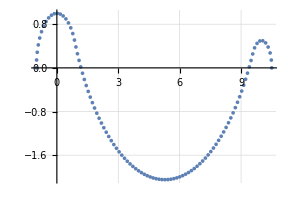
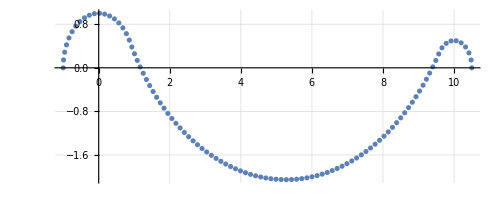
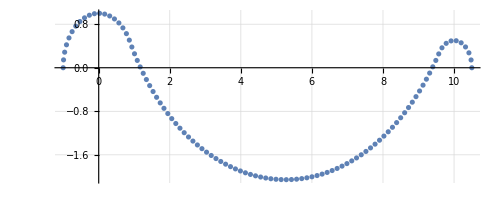
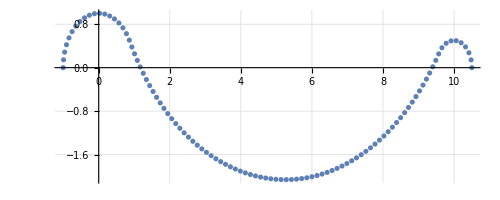
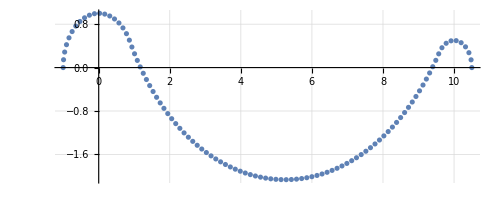

```mathematica
alp1 = -Pi/3.;bet1=-Pi/3.1;
alp2 = -Pi/6.;bet2=-Pi/8.;
gam2 = 0.003;
Reap[Do[Sow[
f[{alp1,bet1,gam1,alp2,bet2,gam2}]],{gam1,0.00001,gMax[alp1,bet1],0.1}]][[2,1]]
```

```mathematica
alp1 = .11;bet1=-0.1;
alp2 = -Pi/6.;bet2=-Pi/8.;
gam2 = 0.003;
curve=Reap[
Do[
Do[
Do[
f[{alp1,bet1,gam1,alp2,bet2,gam2}];Sow[{{gam1,alp1,bet1},d}],{gam1,0.0001,gMax[alp1,bet1],0.1}],{alp1,-Pi/2.3,Pi/2.5,0.1Pi}],{bet1,-Pi/2.4,Pi/3.,0.1 Pi}]][[2,1]];
```

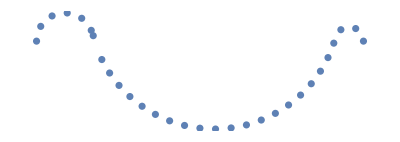
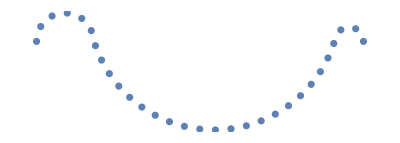
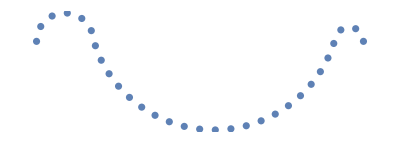
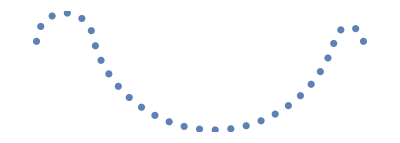
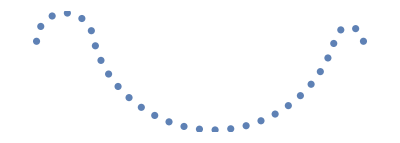
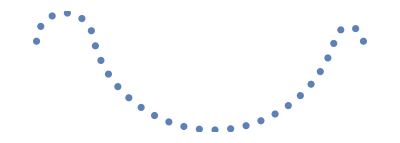
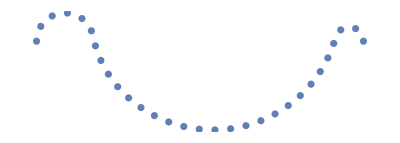
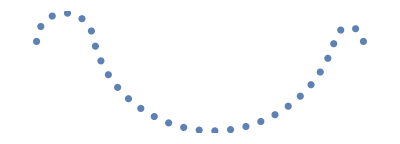
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[#,AspectRatio->{1,1},PlotRange->All,Axes->False]&/@curve[[;;,2]]
```

```mathematica
check[up_,down_]:=Block[{},
eps=10^-4;
flag=0;
Do[
vec=up[[i]]-down[[i]];
If[vec[[2]]<-eps,flag=1;Break[]]
,{i,Length[down]}];
flag
]
```

```mathematica
j=520;
ListPlot[curve[[j,2]],AspectRatio->{1,1},PlotRange->All,Axes->False]
```

-Graphics-

```mathematica
up = curve[[j,2]];
mesh=Reap[Do[
down=curve[[i,2]];
down[[;;,2]]=-down[[;;,2]];
Sow[{curve[[i,1]],check[up,down]}],{i,Length[curve]}]][[2,1]];
```

```mathematica
bad=Select[mesh,#[[2]]==1&][[;;,1]];good=Select[mesh,#[[2]]==0&][[;;,1]];
ListPointPlot3D[{good,bad},AxesLabel->{"gam","alp","bet"}]
```

-Graphics3D-

```mathematica
ListPlot[{down,up},AspectRatio->{1,1}]
```

-Graphics-